

```mathematica
Plot[Sin[x],{x,0,2Pi}]
```

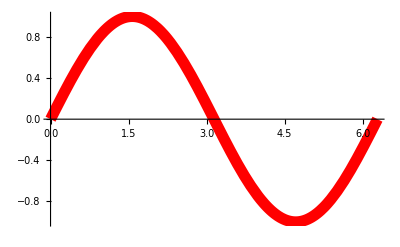

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle-> {Red,Thickness[0.02]}]
```

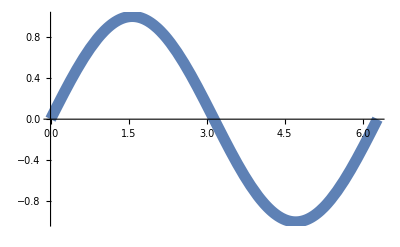

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle-> {ColorData["ThermometerColors"],Thickness[0.02]}]
```

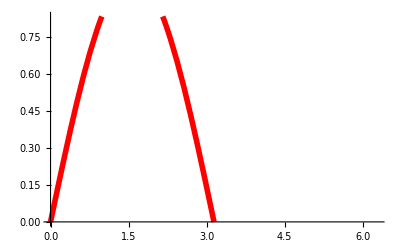

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle-> {Red,Thickness[0.01]},PlotRange->{0,5/6}]
```

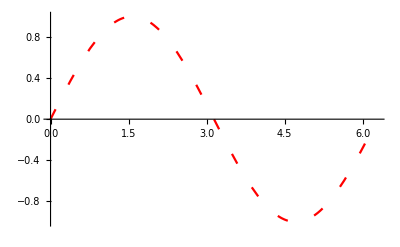

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle-> {Red,Dashing[{0.02,0.05}]}]
```

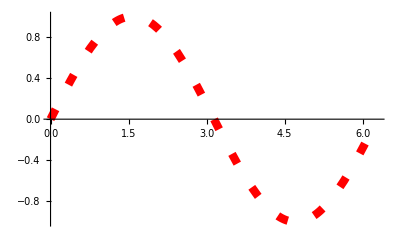

```mathematica
Plot[Sin[x],{x,0,2Pi},PlotStyle-> {Red,Dashing[{0.02,0.05}],Thickness[0.015]}]
```

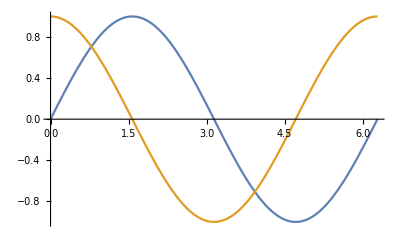

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi}]
```

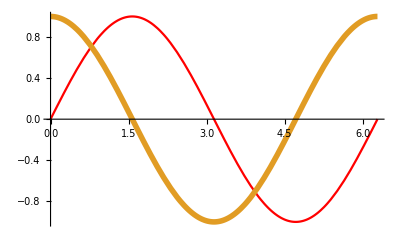

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->{Red,Thickness[0.01]}]
```

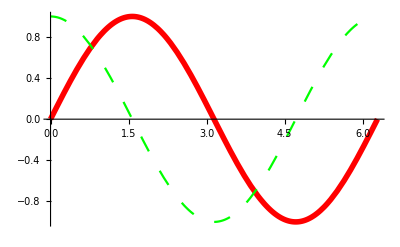

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},PlotStyle->{{Red,Thickness[0.01]},{Green,Dashing[{0.03,0.04}]}}]
```

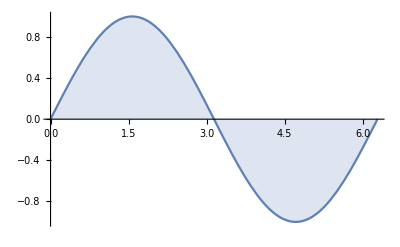

```mathematica
Plot[Sin[x],{x,0,2Pi},Filling-> Axis]
```

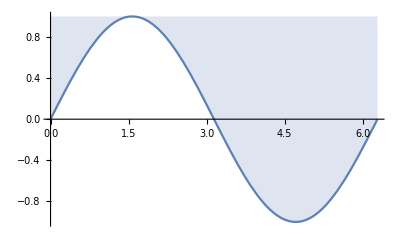

```mathematica
Plot[Sin[x],{x,0,2Pi},Filling-> Top]
```

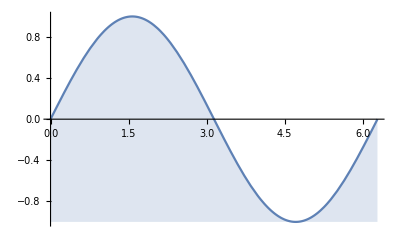

```mathematica
Plot[Sin[x],{x,0,2Pi},Filling-> Bottom]
```

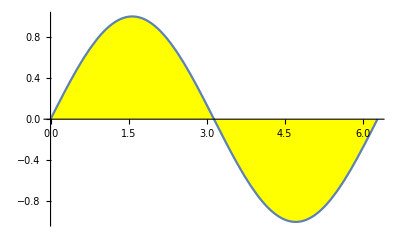

```mathematica
Plot[Sin[x],{x,0,2Pi},Filling-> {1-> {Axis,Yellow}}]
```

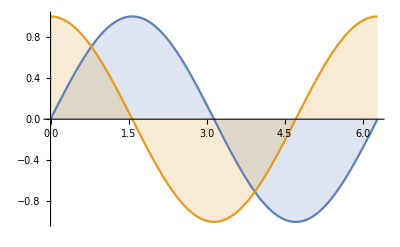

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling-> Axis]
```

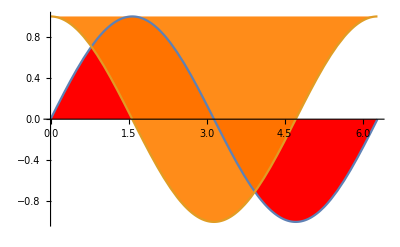

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{{1-> {Axis,Red}},{2->{Top,Opacity[0.9,Orange]}}}]
```

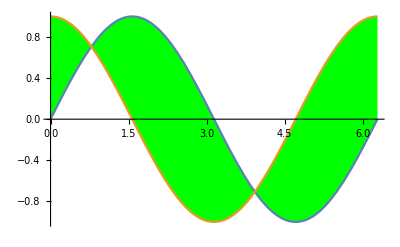

```mathematica
Plot[{Sin[x],Cos[x]},{x,0,2Pi},Filling->{1->{{2},Green}}]
```

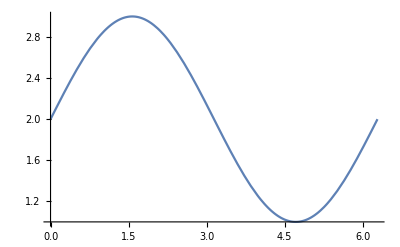

```mathematica
Plot[Sin[x]+2,{x,0,2Pi}]
```

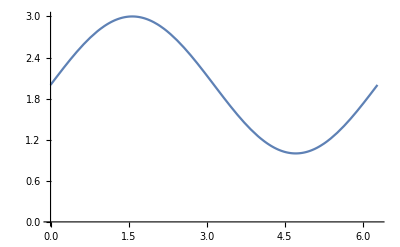

```mathematica
Plot[Sin[x]+2,{x,0,2Pi},AxesOrigin->{0,0}]
```

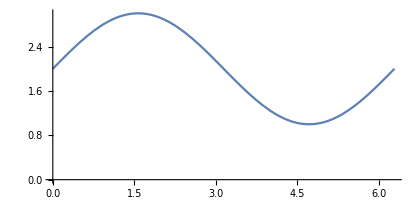

```mathematica
Plot[Sin[x]+2,{x,0,2Pi},AxesOrigin->{0,0},AspectRatio->Automatic]
```

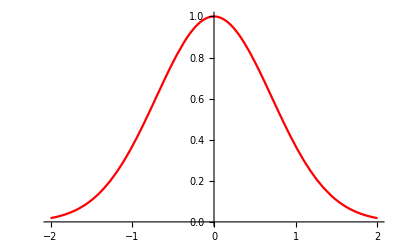

```mathematica
p1=Plot[Exp[-x^2],{x,-2,2},PlotStyle->Red]
```

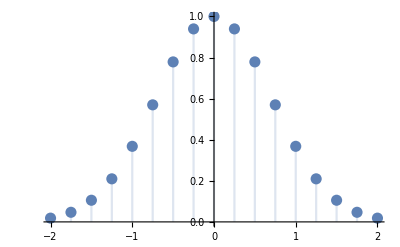

```mathematica
p2=DiscretePlot[Exp[-x^2],{x,-2,2,0.25},PlotStyle-> {PointSize[0.02]}]
```

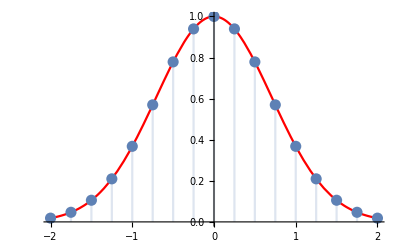

```mathematica
Show[p1,p2]
```

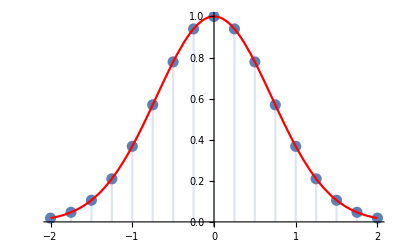

```mathematica
Show[p2,p1]
```

```mathematica
dane=Table[{x,x^2},{x,-2,2,0.2}]
```

{{-2.,4.},{-1.8,3.24},{-1.6,2.56},{-1.4,1.96},{-1.2,1.44},{-1.,1.},{-0.8,0.64},{-0.6,0.36},{-0.4,0.16},{-0.2,0.04},{0.,0.},{0.2,0.04},{0.4,0.16},{0.6,0.36},{0.8,0.64},{1.,1.},{1.2,1.44},{1.4,1.96},{1.6,2.56},{1.8,3.24},{2.,4.}}

x = -2 (x <= 2) {-2, 4}
x = x + 0.2 = -1.8 (x <= 2) {-1.8, 3.24}
 ...
x = x + 0.2 = 2 (x <= 2) {2, 4}
x = x + 0.2 = 2.2 (x <= 2) False

x >= 2

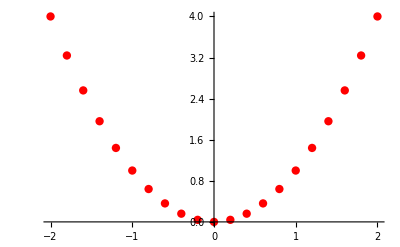

```mathematica
p3=ListPlot[dane,PlotStyle->{Red,PointSize[0.015]}]
```

```mathematica
p4=Plot[x^2,{x,-2,2}];
```

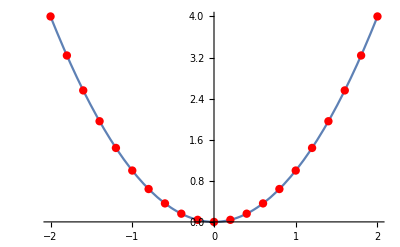

```mathematica
Show[p4,p3]
```

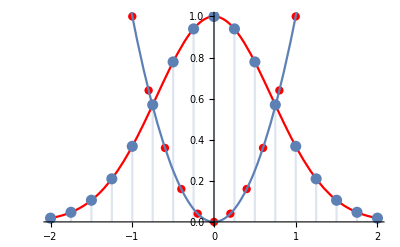

```mathematica
Show[p1,p2,p3,p4]
```

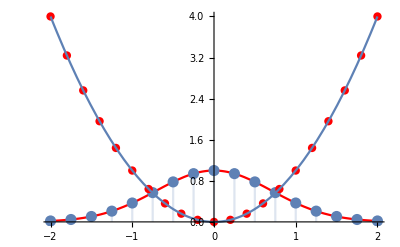

```mathematica
Show[p1,p2,p3,p4,PlotRange->All]
```

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2.2,2}]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x*y],{x,1,4},{y,0,4}]
```

-Graphics3D-

```mathematica
Plot3D[Cos[x*y],{x,1,4},{y,0,4},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2.2,2},Mesh->False]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2.2,2},Mesh->False,Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2.2,2},ColorFunction-> Hue]
```

-Graphics3D-

```mathematica
Plot3D[Exp[-x^2-y^2],{x,-2,2},{y,-2.2,2},ColorFunction-> ColorData["GreenPinkTones"]]
```

-Graphics3D-

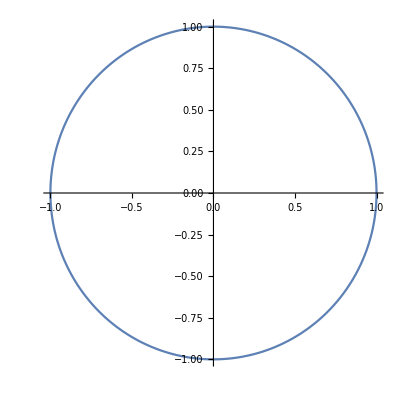

```mathematica
ParametricPlot[{Sin[t],Cos[t]},{t,0,2Pi}]
```

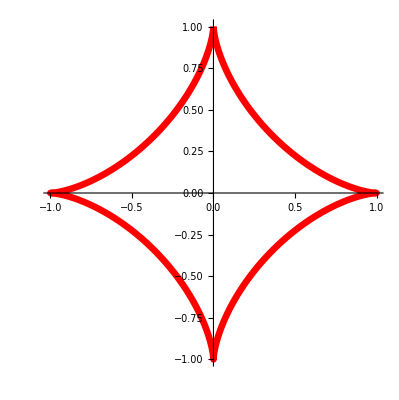

```mathematica
ParametricPlot[{(Sin[t])^3,(Cos[t])^3},{t,0,2Pi},PlotStyle->{Red,Thickness[0.012]}]
```

```mathematica
ParametricPlot3D[{Sin[t],Cos[t],t/4},{t,0,20},PlotStyle->Green]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{Cos[t]Cos[u],Sin[t]Cos[u],Sin[u]},{t,0,2Pi},{u,-Pi/2,Pi/2},ColorFunction->Hue]
```

-Graphics3D-

```mathematica
Animate[Plot[Exp[Sin[x*t]],{x,-Pi,Pi},PlotRange->{0,3}],{t,0,10}]
```

```mathematica
Animate[Plot3D[Sin[a*(x+y)]+Cos[b*(x+y)],{x,0,2Pi},{y,0,Pi},PlotPoints->50],{a,0,4},{b,-2,2}]
```